```mathematica
Quit[]
```

## Input

```mathematica
<<"/home/riccardo/Programs/FeynArts/FeynArts-3.11/FeynArts.m"
```

FeynArts 3.11 (25 Mar 2022)

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

```mathematica
<<"/home/riccardo/Documents/Tesi/ABISS/ABISS.m"
```

+++++ ABISS` +++++
Version 1.0.0

Amplitudes Builder, Interference Solver and Simplifier

Set the path of the Folder where to save final results and temporary results:

```mathematica
SetPath[NotebookDirectory[]];
```

Define the process:

```mathematica
SetProcess[{V[1]}->{V[1]}];
```

Generate default Input files

```mathematica
GenerateInput[];
```

Input file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies/input/kinematics.m already exist. It will NOT be overwritten.

Input file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies/input/integral_families.m already exist. It will NOT be overwritten.

Import the input files (kinematics+integral families).

```mathematica
ImportInput[];
```

Imported input file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies/input/integral_families.m.

Imported input file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies/input/kinematics.m.

## Diagrams generation

Generate diagrams using feynarts (charged current drell-yan, one loop boxes and born).

```mathematica
SetOptions[InsertFields,  Model -> "/home/riccardo/Documents/Tesi/ABISS/models/SMbgf_Anglerfish", GenericModel ->"Lorentzbgf", InsertionLevel->{Particles}, Restrictions->{NoQuarkMixing,NoLightFHCoupling}, ExcludeParticles-> {}];
```

```mathematica
process={V[1]}->{V[1]};
```

```mathematica
topologiesBorn=CreateTopologies[0,1-> 1];
```

```mathematica
fieldsBorn=InsertFields[topologiesBorn, process];
```

loading generic model file /home/riccardo/Programs/FeynArts/FeynArts-3.11/Models/Lorentzbgf.gen

> $GenericMixing is OFF

generic model {Lorentzbgf} initialized

loading classes model file /home/riccardo/Documents/Tesi/ABISS/models/SMbgf_Anglerfish.mod

> 60 particles (incl. antiparticles) in 24 classes

> $CounterTerms are ON

> 689 vertices

> 334 counterterms of order 1

> 2 counterterms of order 2

classes model {/home/riccardo/Documents/Tesi/ABISS/models/SMbgf_Anglerfish} initialized

Excluding 48 field point(s) (incl. charge-conjugate ones)

Restoring 48 field point(s)

in total: 0 Particles insertions

```mathematica
topologies1L=CreateTopologies[1,1-> 1];
```

```mathematica
fields1L=InsertFields[topologies1L, process];
```

Excluding 48 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Particles}

> Top. 1: 2 Particles insertions

> Top. 2: 0 Particles insertions

> Top. 3: 15 Particles insertions

Restoring 48 field point(s)

in total: 17 Particles insertions

```mathematica
amp1L=CreateFeynAmp[fields1L];
```

creating amplitudes at level(s) {Particles}

> Top. 1: 2 Particles amplitudes

> Top. 2: 15 Particles amplitudes

in total: 17 Particles amplitudes

```mathematica
ampBorn=CreateFeynAmp[fieldsBorn];
```

creating amplitudes at level(s) {Particles}

in total: 0 Particles amplitudes

```mathematica
Paint[fieldsBorn]
```

> Top. 1 ac/bc/cc.m, 0 diagrams

> Top. 2 ac/bd/cdcd.m, 0 diagrams

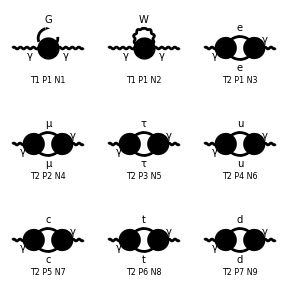

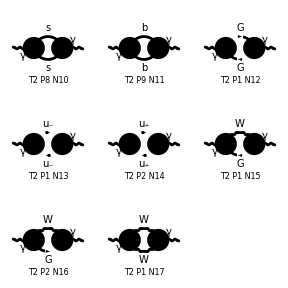

FeynArtsGraphics[{\gamma}→{\gamma}][([T1 P1 N1] | [T1 P1 N2] | [T2 P1 N3]
[T2 P2 N4] | [T2 P3 N5] | [T2 P4 N6]
[T2 P5 N7] | [T2 P6 N8] | [T2 P7 N9]),([T2 P8 N10] | [T2 P9 N11] | [T2 P1 N12]
[T2 P1 N13] | [T2 P2 N14] | [T2 P1 N15]
[T2 P2 N16] | [T2 P1 N17] | Null)]

```mathematica
Paint[fields1L]
```

Extract amplitudes in a Abiss-friendly format, then save them. Put desired masses to zero by hand.

```mathematica
massesToZero={};
```

```mathematica
myAmp1L=ExtractAmplitude[amp1L]/.massesToZero;
myAmpBorn=ExtractAmplitude[ampBorn]/.massesToZero;
```

```mathematica
SaveAmplitudes[myAmp1L,"OneLoopAmplitudes.m"];
SaveAmplitudes[myAmpBorn,"BornAmplitudes.m"];
```

Amplitudes saved in /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies/feynArts_amplitudes/OneLoopAmplitudes.m

Amplitudes saved in /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies/feynArts_amplitudes/BornAmplitudes.m

## Interference

Compute a single interference term “by hand”:

```mathematica
test=AmpSquare[myAmp1L[[1]],myAmp1L[[1]]];
Simplify[test]
```

1/(256 π^8)EL^4 gFFAA^2 KiraPropagator[q1,MW]^2 ep[V[1],p1,{Lor1}] ep[V[1],p1,{newLor1}] ep[V[1],p2,{newLor2}] SP[{Lor1},{Lor2}] SP[{newLor1},{newLor2}] ep^*[V[1],p2,{Lor2}]

Compute all interference term automatically (in this case, also simplifying). Files are saved as Contribution_i_j.m. An optional argument modifies the file name.

```mathematica
SquareSimplifyAndSave[myAmp1L,myAmp1L]
```

Computed contribution 1-1.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_1_1.m.

Computed contribution 1-2.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_1_2.m.

Computed contribution 1-3.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_1_3.m.

Computed contribution 1-4.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_1_4.m.

Computed contribution 1-5.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_1_5.m.

Computed contribution 1-6.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_1_6.m.

Computed contribution 1-7.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_1_7.m.

Computed contribution 1-8.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_1_8.m.

Computed contribution 1-9.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_1_9.m.

Computed contribution 1-10.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_1_10.m.

Computed contribution 1-11.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_1_11.m.

Computed contribution 1-12.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_1_12.m.

Computed contribution 1-13.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_1_13.m.

Computed contribution 1-14.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_1_14.m.

Computed contribution 1-15.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_1_15.m.

Computed contribution 1-16.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_1_16.m.

Computed contribution 1-17.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_1_17.m.

Computed contribution 2-1.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_2_1.m.

Computed contribution 2-2.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_2_2.m.

Computed contribution 2-3.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_2_3.m.

Computed contribution 2-4.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_2_4.m.

Computed contribution 2-5.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_2_5.m.

Computed contribution 2-6.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_2_6.m.

Computed contribution 2-7.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_2_7.m.

Computed contribution 2-8.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_2_8.m.

Computed contribution 2-9.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_2_9.m.

Computed contribution 2-10.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_2_10.m.

Computed contribution 2-11.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_2_11.m.

Computed contribution 2-12.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_2_12.m.

Computed contribution 2-13.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_2_13.m.

Computed contribution 2-14.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_2_14.m.

Computed contribution 2-15.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_2_15.m.

Computed contribution 2-16.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_2_16.m.

Computed contribution 2-17.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_2_17.m.

Computed contribution 3-1.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_3_1.m.

Computed contribution 3-2.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_3_2.m.

Computed contribution 3-3.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_3_3.m.

Computed contribution 3-4.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_3_4.m.

Computed contribution 3-5.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_3_5.m.

Computed contribution 3-6.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_3_6.m.

Computed contribution 3-7.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_3_7.m.

Computed contribution 3-8.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_3_8.m.

Computed contribution 3-9.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_3_9.m.

Computed contribution 3-10.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_3_10.m.

Computed contribution 3-11.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_3_11.m.

Computed contribution 3-12.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_3_12.m.

Computed contribution 3-13.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_3_13.m.

Computed contribution 3-14.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_3_14.m.

Computed contribution 3-15.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_3_15.m.

Computed contribution 3-16.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_3_16.m.

Computed contribution 3-17.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_3_17.m.

Computed contribution 4-1.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_4_1.m.

Computed contribution 4-2.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_4_2.m.

Computed contribution 4-3.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_4_3.m.

Computed contribution 4-4.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_4_4.m.

Computed contribution 4-5.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_4_5.m.

Computed contribution 4-6.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_4_6.m.

Computed contribution 4-7.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_4_7.m.

Computed contribution 4-8.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_4_8.m.

Computed contribution 4-9.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_4_9.m.

Computed contribution 4-10.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_4_10.m.

Computed contribution 4-11.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_4_11.m.

Computed contribution 4-12.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_4_12.m.

Computed contribution 4-13.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_4_13.m.

Computed contribution 4-14.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_4_14.m.

Computed contribution 4-15.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_4_15.m.

Computed contribution 4-16.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_4_16.m.

Computed contribution 4-17.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_4_17.m.

Computed contribution 5-1.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_5_1.m.

Computed contribution 5-2.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_5_2.m.

Computed contribution 5-3.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_5_3.m.

Computed contribution 5-4.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_5_4.m.

Computed contribution 5-5.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_5_5.m.

Computed contribution 5-6.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_5_6.m.

Computed contribution 5-7.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_5_7.m.

Computed contribution 5-8.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_5_8.m.

Computed contribution 5-9.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_5_9.m.

Computed contribution 5-10.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_5_10.m.

Computed contribution 5-11.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_5_11.m.

Computed contribution 5-12.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_5_12.m.

Computed contribution 5-13.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_5_13.m.

Computed contribution 5-14.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_5_14.m.

Computed contribution 5-15.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_5_15.m.

Computed contribution 5-16.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_5_16.m.

Computed contribution 5-17.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_5_17.m.

Computed contribution 6-1.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_6_1.m.

Computed contribution 6-2.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_6_2.m.

Computed contribution 6-3.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_6_3.m.

Computed contribution 6-4.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_6_4.m.

Computed contribution 6-5.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_6_5.m.

Computed contribution 6-6.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_6_6.m.

Computed contribution 6-7.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_6_7.m.

Computed contribution 6-8.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_6_8.m.

Computed contribution 6-9.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_6_9.m.

Computed contribution 6-10.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_6_10.m.

Computed contribution 6-11.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_6_11.m.

Computed contribution 6-12.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_6_12.m.

Computed contribution 6-13.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_6_13.m.

Computed contribution 6-14.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_6_14.m.

Computed contribution 6-15.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_6_15.m.

Computed contribution 6-16.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_6_16.m.

Computed contribution 6-17.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_6_17.m.

Computed contribution 7-1.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_7_1.m.

Computed contribution 7-2.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_7_2.m.

Computed contribution 7-3.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_7_3.m.

Computed contribution 7-4.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_7_4.m.

Computed contribution 7-5.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_7_5.m.

Computed contribution 7-6.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_7_6.m.

Computed contribution 7-7.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_7_7.m.

Computed contribution 7-8.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_7_8.m.

Computed contribution 7-9.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_7_9.m.

Computed contribution 7-10.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_7_10.m.

Computed contribution 7-11.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_7_11.m.

Computed contribution 7-12.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_7_12.m.

Computed contribution 7-13.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_7_13.m.

Computed contribution 7-14.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_7_14.m.

Computed contribution 7-15.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_7_15.m.

Computed contribution 7-16.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_7_16.m.

Computed contribution 7-17.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_7_17.m.

Computed contribution 8-1.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_8_1.m.

Computed contribution 8-2.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_8_2.m.

Computed contribution 8-3.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_8_3.m.

Computed contribution 8-4.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_8_4.m.

Computed contribution 8-5.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_8_5.m.

Computed contribution 8-6.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_8_6.m.

Computed contribution 8-7.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_8_7.m.

Computed contribution 8-8.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_8_8.m.

Computed contribution 8-9.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_8_9.m.

Computed contribution 8-10.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_8_10.m.

Computed contribution 8-11.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_8_11.m.

Computed contribution 8-12.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_8_12.m.

Computed contribution 8-13.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_8_13.m.

Computed contribution 8-14.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_8_14.m.

Computed contribution 8-15.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_8_15.m.

Computed contribution 8-16.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_8_16.m.

Computed contribution 8-17.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_8_17.m.

Computed contribution 9-1.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_9_1.m.

Computed contribution 9-2.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_9_2.m.

Computed contribution 9-3.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_9_3.m.

Computed contribution 9-4.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_9_4.m.

Computed contribution 9-5.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_9_5.m.

Computed contribution 9-6.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_9_6.m.

Computed contribution 9-7.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_9_7.m.

Computed contribution 9-8.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_9_8.m.

Computed contribution 9-9.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_9_9.m.

Computed contribution 9-10.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_9_10.m.

Computed contribution 9-11.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_9_11.m.

Computed contribution 9-12.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_9_12.m.

Computed contribution 9-13.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_9_13.m.

Computed contribution 9-14.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_9_14.m.

Computed contribution 9-15.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_9_15.m.

Computed contribution 9-16.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_9_16.m.

Computed contribution 9-17.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_9_17.m.

Computed contribution 10-1.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_10_1.m.

Computed contribution 10-2.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_10_2.m.

Computed contribution 10-3.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_10_3.m.

Computed contribution 10-4.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_10_4.m.

Computed contribution 10-5.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_10_5.m.

Computed contribution 10-6.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_10_6.m.

Computed contribution 10-7.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_10_7.m.

Computed contribution 10-8.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_10_8.m.

Computed contribution 10-9.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_10_9.m.

Computed contribution 10-10.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_10_10.m.

Computed contribution 10-11.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_10_11.m.

Computed contribution 10-12.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_10_12.m.

Computed contribution 10-13.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_10_13.m.

Computed contribution 10-14.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_10_14.m.

Computed contribution 10-15.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_10_15.m.

Computed contribution 10-16.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_10_16.m.

Computed contribution 10-17.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_10_17.m.

Computed contribution 11-1.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_11_1.m.

Computed contribution 11-2.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_11_2.m.

Computed contribution 11-3.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_11_3.m.

Computed contribution 11-4.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_11_4.m.

Computed contribution 11-5.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_11_5.m.

Computed contribution 11-6.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_11_6.m.

Computed contribution 11-7.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_11_7.m.

Computed contribution 11-8.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_11_8.m.

Computed contribution 11-9.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_11_9.m.

Computed contribution 11-10.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_11_10.m.

Computed contribution 11-11.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_11_11.m.

Computed contribution 11-12.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_11_12.m.

Computed contribution 11-13.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_11_13.m.

Computed contribution 11-14.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_11_14.m.

Computed contribution 11-15.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_11_15.m.

Computed contribution 11-16.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_11_16.m.

Computed contribution 11-17.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_11_17.m.

Computed contribution 12-1.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_12_1.m.

Computed contribution 12-2.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_12_2.m.

Computed contribution 12-3.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_12_3.m.

Computed contribution 12-4.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_12_4.m.

Computed contribution 12-5.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_12_5.m.

Computed contribution 12-6.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_12_6.m.

Computed contribution 12-7.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_12_7.m.

Computed contribution 12-8.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_12_8.m.

Computed contribution 12-9.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_12_9.m.

Computed contribution 12-10.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_12_10.m.

Computed contribution 12-11.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_12_11.m.

Computed contribution 12-12.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_12_12.m.

Computed contribution 12-13.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_12_13.m.

Computed contribution 12-14.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_12_14.m.

Computed contribution 12-15.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_12_15.m.

Computed contribution 12-16.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_12_16.m.

Computed contribution 12-17.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_12_17.m.

Computed contribution 13-1.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_13_1.m.

Computed contribution 13-2.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_13_2.m.

Computed contribution 13-3.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_13_3.m.

Computed contribution 13-4.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_13_4.m.

Computed contribution 13-5.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_13_5.m.

Computed contribution 13-6.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_13_6.m.

Computed contribution 13-7.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_13_7.m.

Computed contribution 13-8.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_13_8.m.

Computed contribution 13-9.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_13_9.m.

Computed contribution 13-10.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_13_10.m.

Computed contribution 13-11.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_13_11.m.

Computed contribution 13-12.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_13_12.m.

Computed contribution 13-13.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_13_13.m.

Computed contribution 13-14.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_13_14.m.

Computed contribution 13-15.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_13_15.m.

Computed contribution 13-16.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_13_16.m.

Computed contribution 13-17.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_13_17.m.

Computed contribution 14-1.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_14_1.m.

Computed contribution 14-2.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_14_2.m.

Computed contribution 14-3.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_14_3.m.

Computed contribution 14-4.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_14_4.m.

Computed contribution 14-5.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_14_5.m.

Computed contribution 14-6.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_14_6.m.

Computed contribution 14-7.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_14_7.m.

Computed contribution 14-8.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_14_8.m.

Computed contribution 14-9.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_14_9.m.

Computed contribution 14-10.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_14_10.m.

Computed contribution 14-11.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_14_11.m.

Computed contribution 14-12.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_14_12.m.

Computed contribution 14-13.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_14_13.m.

Computed contribution 14-14.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_14_14.m.

Computed contribution 14-15.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_14_15.m.

Computed contribution 14-16.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_14_16.m.

Computed contribution 14-17.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_14_17.m.

Computed contribution 15-1.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_15_1.m.

Computed contribution 15-2.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_15_2.m.

Computed contribution 15-3.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_15_3.m.

Computed contribution 15-4.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_15_4.m.

Computed contribution 15-5.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_15_5.m.

Computed contribution 15-6.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_15_6.m.

Computed contribution 15-7.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_15_7.m.

Computed contribution 15-8.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_15_8.m.

Computed contribution 15-9.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_15_9.m.

Computed contribution 15-10.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_15_10.m.

Computed contribution 15-11.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_15_11.m.

Computed contribution 15-12.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_15_12.m.

Computed contribution 15-13.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_15_13.m.

Computed contribution 15-14.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_15_14.m.

Computed contribution 15-15.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_15_15.m.

Computed contribution 15-16.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_15_16.m.

Computed contribution 15-17.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_15_17.m.

Computed contribution 16-1.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_16_1.m.

Computed contribution 16-2.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_16_2.m.

Computed contribution 16-3.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_16_3.m.

Computed contribution 16-4.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_16_4.m.

Computed contribution 16-5.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_16_5.m.

Computed contribution 16-6.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_16_6.m.

Computed contribution 16-7.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_16_7.m.

Computed contribution 16-8.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_16_8.m.

Computed contribution 16-9.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_16_9.m.

Computed contribution 16-10.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_16_10.m.

Computed contribution 16-11.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_16_11.m.

Computed contribution 16-12.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_16_12.m.

Computed contribution 16-13.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_16_13.m.

Computed contribution 16-14.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_16_14.m.

Computed contribution 16-15.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_16_15.m.

Computed contribution 16-16.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_16_16.m.

Computed contribution 16-17.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_16_17.m.

Computed contribution 17-1.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_17_1.m.

Computed contribution 17-2.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_17_2.m.

Computed contribution 17-3.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_17_3.m.

Computed contribution 17-4.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_17_4.m.

Computed contribution 17-5.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_17_5.m.

Computed contribution 17-6.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_17_6.m.

Computed contribution 17-7.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_17_7.m.

Computed contribution 17-8.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_17_8.m.

Computed contribution 17-9.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_17_9.m.

Computed contribution 17-10.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_17_10.m.

Computed contribution 17-11.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_17_11.m.

Computed contribution 17-12.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_17_12.m.

Computed contribution 17-13.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_17_13.m.

Computed contribution 17-14.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_17_14.m.

Computed contribution 17-15.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_17_15.m.

Computed contribution 17-16.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_17_16.m.

Computed contribution 17-17.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies//interferences/Contribution_17_17.m.

## Shift

Perform the shift to one of the integral families in the input file. Please use the following input file for this test:

userLoopMomenta={
q1
};
(*User-defined integral families*)
userIntegralFamiliesNames={
TopoCM,
TopoCMp,
TopoC2M,
TopoC2Mp
};
userPropagatorMomenta[TopoCM]={
	q1,
	-p1+q1,
	p2+q1,
	p3-p1+q1
};

userIntegralMasses[TopoCM]={0,M1,0,0};

userPropagatorMomenta[TopoCMp]={
	q1,
	-p1+q1,
	p2+q1,
	-p3+p2+q1
};

userIntegralMasses[TopoCMp]={0,0,M1,0};

userPropagatorMomenta[TopoC2M]={
	q1,
	-p1+q1,
	p2+q1,
	p3-p1+q1
};

userIntegralMasses[TopoC2M]={0,M1,M2,0};

userPropagatorMomenta[TopoC2Mp]={
	q1,
	-p1+q1,
	p2+q1,
	-p3+p2+q1
};

userIntegralMasses[TopoC2Mp]={0,M1,M2,0};

The shift can be done by hand.
Use ExtractFamily to check if an expression is already recognised as one of the integral families. Our test is already written in terms off an integral family:

```mathematica
ExtractFamily[test]
```

{False}

Now let us define an expression which cannot be immediately recognised:

```mathematica
test2=test/.{q1-> -q1+p1};
ExtractFamily[test2]
```

{False}

The shift to write it in terms of integral families can be obtained with ShiftToIntegralFamily:

```mathematica
ShiftToIntegralFamily[test2]
ExtractFamily[test/.%]
```

{False}

ReplaceAll::reps: {False} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

{False}

The shift can also be done automatically with ShiftAndSave. The flag indicates if to overwrite (True) or not (False, generates another folder with the result before the shift) the result. Files are saved as Contribution_i_j.m. An optional argument modifies the file name.

```mathematica
Do[
ShiftAndSave[i,j,False];
,{i,6},{j,1}]
```

First::nofirst: \!\(\*RowBox[{"{", "}"}]\) has zero length and no first element.

ReplaceAll::reps: \!\(\*RowBox[{"{", RowBox[{"First", "[", RowBox[{"{", "}"}], "]"}], "}"}]\) is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

First::nofirst: \!\(\*RowBox[{"{", "}"}]\) has zero length and no first element.

ReplaceAll::reps: \!\(\*RowBox[{"{", RowBox[{"First", "[", RowBox[{"{", "}"}], "]"}], "}"}]\) is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

First::nofirst: \!\(\*RowBox[{"{", "}"}]\) has zero length and no first element.

General::stop: Further output of \!\(\*StyleBox[RowBox[{"First", "::", "nofirst"}], "MessageName"]\) will be suppressed during this calculation.

ReplaceAll::reps: \!\(\*RowBox[{"{", RowBox[{"First", "[", RowBox[{"{", "}"}], "]"}], "}"}]\) is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of \!\(\*StyleBox[RowBox[{"ReplaceAll", "::", "reps"}], "MessageName"]\) will be suppressed during this calculation.

ERROR: missing integral family for /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies/interferences/Contribution_1_1.m.

ERROR: missing integral family for /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies/interferences/Contribution_2_1.m.

ERROR: missing integral family for /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies/interferences/Contribution_3_1.m.

ERROR: missing integral family for /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies/interferences/Contribution_4_1.m.

ERROR: missing integral family for /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies/interferences/Contribution_5_1.m.

ERROR: missing integral family for /home/riccardo/Documents/Tesi/TestABISS/SelfEnergies/interferences/Contribution_6_1.m.

## KiraInput

Can be done by hand on a single term:

```mathematica
test=GenerateKiraInput[test]
```

Part::partw: Part 2 of {False} does not exist.

Intersection::heads: Heads List and userPropagatorMomenta at positions 2 and 1 are expected to be the same.

Join::heads: Heads List and Intersection at positions 1 and 2 are expected to be the same.

Join::heads: Heads Intersection and List at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

Intersection::heads: Heads List and userPropagatorMomenta at positions 2 and 1 are expected to be the same.

Intersection::heads: Heads SP and userPropagatorMomenta at positions 2 and 1 are expected to be the same.

General::stop: Further output of Intersection::heads will be suppressed during this calculation.

Intersection::normal: Nonatomic expression expected at position 2 in userPropagatorMomenta[False]∩0.

Intersection::normal: Nonatomic expression expected at position 2 in userPropagatorMomenta[False]∩0∩userPropagatorMomenta[False]∩0.

General::stop: Further output of Intersection::normal will be suppressed during this calculation.

First::nofirst: {} has zero length and no first element.

ReplaceAll::reps: {First[{}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

1/(256 π^8)EL^4 gFFAA^2 KiraPropagator[q1,MW]^2 ep[V[1],p1,{Lor1}] ep[V[1],p1,{newLor1}] ep[V[1],p2,{newLor2}] SP[{Lor1},{Lor2}] SP[{newLor1},{newLor2}] userIntegral[False,{False}⟦2⟧,0] ep^*[V[1],p2,{Lor2}]

Or automatically, saving the results. Files are saved as Contribution_i_j.m. An optional argument modifies the file name.

```mathematica
Do[
GenerateAndSaveKiraInput[i,j];
,{i,6},{j,1}]
```

Overwritten file /Users/simonedevoto/Physics/Milano/ABISS/example/kira_input/Contribution_1_1.m.

Overwritten file /Users/simonedevoto/Physics/Milano/ABISS/example/kira_input/Contribution_2_1.m.

Overwritten file /Users/simonedevoto/Physics/Milano/ABISS/example/kira_input/Contribution_3_1.m.

Overwritten file /Users/simonedevoto/Physics/Milano/ABISS/example/kira_input/Contribution_4_1.m.

Overwritten file /Users/simonedevoto/Physics/Milano/ABISS/example/kira_input/Contribution_5_1.m.

Overwritten file /Users/simonedevoto/Physics/Milano/ABISS/example/kira_input/Contribution_6_1.m.

The list of scalar integral introduced (and that need to be reduced) can be printed with PrintScalarIntegrals:

```mathematica
PrintScalarIntegrals[]
```

{userIntegral[TopoCM,{MW},-1,1,1,1],userIntegral[TopoCM,{MW},0,0,1,1],userIntegral[TopoCM,{MW},0,1,0,1],userIntegral[TopoCM,{MW},0,1,1,0],userIntegral[TopoCM,{MW},0,1,1,1],userIntegral[TopoCM,{MW},1,-1,1,1],userIntegral[TopoCM,{MW},1,0,0,1],userIntegral[TopoCM,{MW},1,0,1,0],userIntegral[TopoCM,{MW},1,0,1,1],userIntegral[TopoCM,{MW},1,1,-1,1],userIntegral[TopoCM,{MW},1,1,0,0],userIntegral[TopoCM,{MW},1,1,0,1],userIntegral[TopoCM,{MW},1,1,1,-1],userIntegral[TopoCM,{MW},1,1,1,0],userIntegral[TopoCM,{MW},1,1,1,1],userIntegral[TopoC2M,{MZ,MW},-1,1,1,1],userIntegral[TopoC2M,{MZ,MW},0,0,1,1],userIntegral[TopoC2M,{MZ,MW},0,1,0,1],userIntegral[TopoC2M,{MZ,MW},0,1,1,0],userIntegral[TopoC2M,{MZ,MW},0,1,1,1],userIntegral[TopoC2M,{MZ,MW},1,-1,1,1],userIntegral[TopoC2M,{MZ,MW},1,0,0,1],userIntegral[TopoC2M,{MZ,MW},1,0,1,0],userIntegral[TopoC2M,{MZ,MW},1,0,1,1],userIntegral[TopoC2M,{MZ,MW},1,1,-1,1],userIntegral[TopoC2M,{MZ,MW},1,1,0,0],userIntegral[TopoC2M,{MZ,MW},1,1,0,1],userIntegral[TopoC2M,{MZ,MW},1,1,1,-1],userIntegral[TopoC2M,{MZ,MW},1,1,1,0],userIntegral[TopoC2M,{MZ,MW},1,1,1,1],userIntegral[TopoC2M,{MW,MZ},-1,1,1,1],userIntegral[TopoC2M,{MW,MZ},0,0,1,1],userIntegral[TopoC2M,{MW,MZ},0,1,0,1],userIntegral[TopoC2M,{MW,MZ},0,1,1,0],userIntegral[TopoC2M,{MW,MZ},0,1,1,1],userIntegral[TopoC2M,{MW,MZ},1,-1,1,1],userIntegral[TopoC2M,{MW,MZ},1,0,0,1],userIntegral[TopoC2M,{MW,MZ},1,0,1,0],userIntegral[TopoC2M,{MW,MZ},1,0,1,1],userIntegral[TopoC2M,{MW,MZ},1,1,-1,1],userIntegral[TopoC2M,{MW,MZ},1,1,0,0],userIntegral[TopoC2M,{MW,MZ},1,1,0,1],userIntegral[TopoC2M,{MW,MZ},1,1,1,-1],userIntegral[TopoC2M,{MW,MZ},1,1,1,0],userIntegral[TopoC2M,{MW,MZ},1,1,1,1],userIntegral[TopoCMp,{MW},-1,1,1,1],userIntegral[TopoCMp,{MW},0,0,1,1],userIntegral[TopoCMp,{MW},0,1,0,1],userIntegral[TopoCMp,{MW},0,1,1,0],userIntegral[TopoCMp,{MW},0,1,1,1],userIntegral[TopoCMp,{MW},1,-1,1,1],userIntegral[TopoCMp,{MW},1,0,0,1],userIntegral[TopoCMp,{MW},1,0,1,0],userIntegral[TopoCMp,{MW},1,0,1,1],userIntegral[TopoCMp,{MW},1,1,-1,1],userIntegral[TopoCMp,{MW},1,1,0,0],userIntegral[TopoCMp,{MW},1,1,0,1],userIntegral[TopoCMp,{MW},1,1,1,-1],userIntegral[TopoCMp,{MW},1,1,1,0],userIntegral[TopoCMp,{MW},1,1,1,1],userIntegral[TopoC2Mp,{MZ,MW},-1,1,1,1],userIntegral[TopoC2Mp,{MZ,MW},0,0,1,1],userIntegral[TopoC2Mp,{MZ,MW},0,1,0,1],userIntegral[TopoC2Mp,{MZ,MW},0,1,1,0],userIntegral[TopoC2Mp,{MZ,MW},0,1,1,1],userIntegral[TopoC2Mp,{MZ,MW},1,-1,1,1],userIntegral[TopoC2Mp,{MZ,MW},1,0,0,1],userIntegral[TopoC2Mp,{MZ,MW},1,0,1,0],userIntegral[TopoC2Mp,{MZ,MW},1,0,1,1],userIntegral[TopoC2Mp,{MZ,MW},1,1,-1,1],userIntegral[TopoC2Mp,{MZ,MW},1,1,0,0],userIntegral[TopoC2Mp,{MZ,MW},1,1,0,1],userIntegral[TopoC2Mp,{MZ,MW},1,1,1,-1],userIntegral[TopoC2Mp,{MZ,MW},1,1,1,0],userIntegral[TopoC2Mp,{MZ,MW},1,1,1,1],userIntegral[TopoC2Mp,{MW,MZ},-1,1,1,1],userIntegral[TopoC2Mp,{MW,MZ},0,0,1,1],userIntegral[TopoC2Mp,{MW,MZ},0,1,0,1],userIntegral[TopoC2Mp,{MW,MZ},0,1,1,0],userIntegral[TopoC2Mp,{MW,MZ},0,1,1,1],userIntegral[TopoC2Mp,{MW,MZ},1,-1,1,1],userIntegral[TopoC2Mp,{MW,MZ},1,0,0,1],userIntegral[TopoC2Mp,{MW,MZ},1,0,1,0],userIntegral[TopoC2Mp,{MW,MZ},1,0,1,1],userIntegral[TopoC2Mp,{MW,MZ},1,1,-1,1],userIntegral[TopoC2Mp,{MW,MZ},1,1,0,0],userIntegral[TopoC2Mp,{MW,MZ},1,1,0,1],userIntegral[TopoC2Mp,{MW,MZ},1,1,1,-1],userIntegral[TopoC2Mp,{MW,MZ},1,1,1,0],userIntegral[TopoC2Mp,{MW,MZ},1,1,1,1]}

There are two different ways of saving the scalar integrals. SaveScalarIntegrals saves the list as it is printed by PrintScalarIntegrals, while ExportScalarIntegrals converts it in a Kira-friendly format.

```mathematica
SaveScalarIntegrals["scalar_integrals"];
ExportScalarIntegrals["kira_scalar_integrals.dat"];
```

## Apply Kira sub;

If needed, the scalar integrals can be imported from the file previously saved with SaveScalarIntegrals:

```mathematica
ImportScalarIntegrals["scalar_integrals"];
```

One need to compute externally the substitution rules to write this set of scalar integrals in terms of master integrals.  The internal masses are expected to be called m1, m2, ...
In this example the rules are provided in kira_rules_example.m. We import them:

```mathematica
ImportRules[NotebookDirectory[]<>"kira_rules_example.m"];
```

We perform some change of variables in the rules in order to have a notation uniform with the rest of our computation:

```mathematica
ReplaceInRules[{s-> s12,t-> s23}];
```

If needed, the imported rules can be printed with PrintRules[]. They can be applied to a specific expression with ApplyRules.

```mathematica
test4=ApplyRules[test3];
```

```mathematica
Cases[test3,userIntegral[x___]:> userIntegral[x],Infinity]//DeleteDuplicates
Cases[test4,userIntegral[x___]:> userIntegral[x],Infinity]//DeleteDuplicates
```

{userIntegral[TopoCM,{MW},-1,1,1,1],userIntegral[TopoCM,{MW},0,0,1,1],userIntegral[TopoCM,{MW},0,1,0,1],userIntegral[TopoCM,{MW},0,1,1,0],userIntegral[TopoCM,{MW},0,1,1,1],userIntegral[TopoCM,{MW},1,-1,1,1],userIntegral[TopoCM,{MW},1,0,0,1],userIntegral[TopoCM,{MW},1,0,1,0],userIntegral[TopoCM,{MW},1,0,1,1],userIntegral[TopoCM,{MW},1,1,-1,1],userIntegral[TopoCM,{MW},1,1,0,0],userIntegral[TopoCM,{MW},1,1,0,1],userIntegral[TopoCM,{MW},1,1,1,-1],userIntegral[TopoCM,{MW},1,1,1,0],userIntegral[TopoCM,{MW},1,1,1,1]}

{userIntegral[TopoCM,{MW},0,1,0,0],userIntegral[TopoCM,{MW},0,1,1,0],userIntegral[TopoCM,{MW},1,0,0,1],userIntegral[TopoCM,{MW},1,1,0,1],userIntegral[TopoCM,{MW},1,1,1,1]}

This same set of rules can be used to identify the basis of masters needed to express the scalar integrals previously selected. This is done with DetermineMasterIntegrals:

```mathematica
DetermineMasterIntegrals[]
```

And the set of masters can be printed:

```mathematica
PrintMasterIntegrals[]
```

{userIntegral[TopoCM,{MW},0,1,0,0],userIntegral[TopoCM,{MW},0,1,1,0],userIntegral[TopoCM,{MW},1,0,0,1],userIntegral[TopoCM,{MW},1,1,0,1],userIntegral[TopoCM,{MW},1,1,1,1],userIntegral[TopoC2M,{MZ,MW},0,0,1,0],userIntegral[TopoC2M,{MZ,MW},0,1,1,0],userIntegral[TopoC2M,{MZ,MW},1,1,1,0],userIntegral[TopoCM,{MZ},0,1,0,0],userIntegral[TopoC2M,{MZ,MW},1,0,1,1],userIntegral[TopoCM,{MZ},1,0,0,1],userIntegral[TopoCM,{MZ},1,1,0,1],userIntegral[TopoC2M,{MZ,MW},1,1,1,1],userIntegral[TopoC2M,{MW,MZ},0,0,1,0],userIntegral[TopoC2M,{MW,MZ},0,1,1,0],userIntegral[TopoC2M,{MW,MZ},1,1,1,0],userIntegral[TopoC2M,{MW,MZ},1,0,1,1],userIntegral[TopoC2M,{MW,MZ},1,1,1,1],userIntegral[TopoCMp,{MW},1,0,0,1],userIntegral[TopoCMp,{MW},1,0,1,1],userIntegral[TopoCMp,{MW},1,1,1,1],userIntegral[TopoC2Mp,{MZ,MW},1,0,1,1],userIntegral[TopoCMp,{MZ},1,0,0,1],userIntegral[TopoCMp,{MZ},1,0,1,1],userIntegral[TopoC2Mp,{MZ,MW},1,1,1,1],userIntegral[TopoC2Mp,{MW,MZ},1,0,1,1],userIntegral[TopoC2Mp,{MW,MZ},1,1,1,1]}

The reduction to masters can applied to all the expressions stored in kira_input/ with SaveResult. The output is saved in RESULTS/ as a list of masters and a corresponding set of lists of coefficients. They can then be straightforwardly combined to evaluate a grid.

```mathematica
Do[
SaveResult[i,j];
,{i,6},{j,1}]
```